# Noise in A

## What is the sensitivity of A to gate noise?

Let a particular observable (a factor of an entry in the matrix) have outcome 1 with probability p, else -1 with 1-p.
Let the outcome measurement erroneously flip with probably pe.
The expected value of a particular measurement outcome is then

```mathematica
expecOneSample = 1p pe -1(1-p)(1-pe) // Simplify
```

-1+p+pe

and the variance is

```mathematica
varOneSample = (1^2 p pe + 1^2(1-p)(1-pe)) - expecOneSample^2 // Simplify
```

p-p^2+pe-pe^2

After n samples, the expected value of the mean of the samples is

```mathematica
expecManySample = expecOneSample
```

-1+p+pe

and the variance is

```mathematica
varManySample = varOneSample / n
```

(p-p^2+pe-pe^2)/n

This is maximum when p = 1/2, in which case

```mathematica
varManySample /. p -> 1/2
```

(1/4+pe-pe^2)/n

Let pe be the chance of an odd number of flip errors in the observable, based on a small chance ϵ for every circuit depth d.

```mathematica
Sum[
	PDF[BinomialDistribution[n, ϵ], num],
	{num, 1,d,2}
];
varObsvMean = %% /. pe -> %
```

1/n(1/4+Sum[Piecewise[{{(1-ϵ)^(n-num) ϵ^num Binomial[n,num], 0≤num≤n}, {0, True}}],{num,1,d,2}]-Sum[Piecewise[{{(1-ϵ)^(n-num) ϵ^num Binomial[n,num], 0≤num≤n}, {0, True}}],{num,1,d,2}]^2)

```mathematica
varObsvMean /. {ϵ -> 0.001, n -> 999}
```

1/999(1/4+Sum[Piecewise[{{0.001^num 0.999^(999-num) Binomial[999,num], 0≤num≤999}, {0, True}}],{num,1,d,2}]-Sum[Piecewise[{{0.001^num 0.999^(999-num) Binomial[999,num], 0≤num≤999}, {0, True}}],{num,1,d,2}]^2)

The number of samples n(d, ϵ) needed to keep this variance fixed satisfies

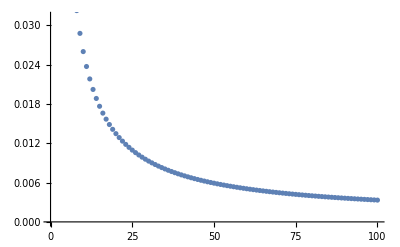

```mathematica
ListPlot @ Table[
	varObsvMean /. {ϵ -> 0.001, d -> 10, n -> nval},
	{nval, 1, 100}
]
```

```mathematica
Sum[
	PDF[BinomialDistribution[n, ϵ], num],
	{num, 1,n,2}
]

Simplify[%, Assumptions-> {0 < ϵ < 1, n ∈ Integers, n > 1}]
```

Sum[Piecewise[{{(1-ϵ)^(n-num) ϵ^num Binomial[n,num], 0≤num≤n}, {0, True}}],{num,1,n,2}]

Sum[Piecewise[{{(1-ϵ)^(n-num) ϵ^num Binomial[n,num], 0≤num≤n}, {0, True}}],{num,1,n,2}]